```mathematica
f1=1/Sqrt[2*π*σ^2]*Exp[-1/2*((x-μ)/σ)^2];
$Assumptions=σ>0;
EV=Integrate[x f1,{x,-Infinity,Infinity}]
Var=Integrate[(x-EV)^2 f1,{x,-Infinity,Infinity}]
Integrate[ReplaceAll[f1,{μ->2.79164,σ->3.313}],{x,10,Infinity}]//N
```

μ

σ^2

0.0147858-9.84528×10^-17 ⅈ

```mathematica
Re[Integrate[ReplaceAll[f1,{μ->2.79164,σ->3.313}],{x,10,Infinity}]]//N
Integrate[ReplaceAll[f1,{μ->2.79164,σ->3.313}],{x,10,1000000000000000000000000000000000000000000000000000000000000000000000000000000}]//N
```

0.0147858

0.0147858

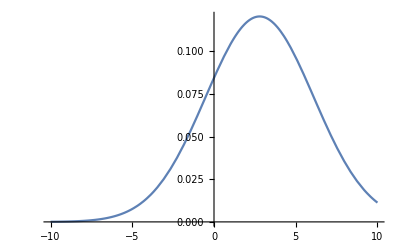

```mathematica
Plot[ReplaceAll[f1,{μ->2.79164,σ->3.313}],{x,-10,10}]
```

```mathematica
Manipulate[
Plot[ReplaceAll[f1,{μ->a,σ->b}],{x,-10,10},PlotRange->{0,1}],
{a,-10,10},{b,0.1,5}
]
```

```mathematica
f=(β^α/Gamma[α])*x^(α-1) Exp[-β*x];
$Assumptions=α>0&&β>0;
EV=Integrate[x f,{x,0,Infinity}]
Var=Integrate[(x-EV)^2 f,{x,0,Infinity}]
Integrate[ReplaceAll[f,{α->0.709823,β->0.2542674}],{x,10,Infinity}]//N
```

α/β

α/β^2

0.0429819

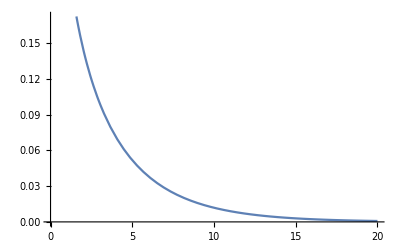

```mathematica
Plot[ReplaceAll[f,{α->0.709823,β->0.2542674}],{x,0,20}]
```

```mathematica
Manipulate[
Plot[ReplaceAll[f,{α->a,β->b}],{x,0,20},PlotRange->{0,1}],
{a,0.1,10},{b,0.1,10}
]
```

```mathematica
f1=1/Sqrt[2*π*σ^2]*Exp[-1/2*((x-μ)/σ)^2];
$Assumptions=σ>0;
μ=21
σ=5
EV=Integrate[x f1,{x,-Infinity,Infinity}]
Var=Integrate[(x-EV)^2 f1,{x,-Infinity,Infinity}]
```

21

5

21

25

```mathematica
Integrate[f1,{x,16,26}]//N
```

0.682689